## Exercícios Lista 4

13.1 Make a 12×12 multiplication table.

```mathematica
Table[x*y,{x,12},{y,12}]
```

{{1,2,3,4,5,6,7,8,9,10,11,12},{2,4,6,8,10,12,14,16,18,20,22,24},{3,6,9,12,15,18,21,24,27,30,33,36},{4,8,12,16,20,24,28,32,36,40,44,48},{5,10,15,20,25,30,35,40,45,50,55,60},{6,12,18,24,30,36,42,48,54,60,66,72},{7,14,21,28,35,42,49,56,63,70,77,84},{8,16,24,32,40,48,56,64,72,80,88,96},{9,18,27,36,45,54,63,72,81,90,99,108},{10,20,30,40,50,60,70,80,90,100,110,120},{11,22,33,44,55,66,77,88,99,110,121,132},{12,24,36,48,60,72,84,96,108,120,132,144}}

13.2 Make a 5×5 multiplication table for Roman numerals.

```mathematica
Table[RomanNumeral[x*y],{x,5},{y,5}]//Grid
```

I | II | III | IV | V
II | IV | VI | VIII | X
III | VI | IX | XII | XV
IV | VIII | XII | XVI | XX
V | X | XV | XX | XXV

13.3 Make a 10×10 grid of random colors.

```mathematica
Grid[Table[RandomColor[],{10},{10}]]
```

RGBColor[0.4024757101486127, 0.7090940931600063, 0.748441137850669] | RGBColor[0.8035468810225601, 0.2399774908749457, 0.8800359284927795] | RGBColor[0.9799267292554814, 0.22139670384756083, 0.31943088331798064] | RGBColor[0.8276341568092356, 0.5144149393587865, 0.665358862876591] | RGBColor[0.712040606294978, 0.2587622450898699, 0.9949959291453747] | RGBColor[0.407855152166102, 0.34370313554008236, 0.5125416832101222] | RGBColor[0.6106583079707946, 0.9495575998966659, 0.5534560072273138] | RGBColor[0.9938094432911644, 0.5566084315307909, 0.11183953236777455] | RGBColor[0.0939756510510592, 0.7981070789730358, 0.9353597119241044] | RGBColor[0.6482909615473627, 0.1706597292652532, 0.14078110981600034]
RGBColor[0.947369764189677, 0.3323818080150811, 0.7147102287870208] | RGBColor[0.61840239163353, 0.7517446236034615, 0.7571610381357567] | RGBColor[0.31978798535525765, 0.9847120089319075, 0.8654457066946812] | RGBColor[0.43015823316849855, 0.9569900190729992, 0.17210349430757543] | RGBColor[0.3677947774919761, 0.3300961129473212, 0.5924960361112375] | RGBColor[0.3123935871933705, 0.488525138615727, 0.7980860548558011] | RGBColor[0.6488084230442701, 0.9901206939871099, 0.5522927193023797] | RGBColor[0.9746187599514764, 0.05492452639428014, 0.12988145679523977] | RGBColor[0.9107038439329571, 0.894064446109583, 0.23452118737060612] | RGBColor[0.24469743939982957, 0.93951040616039, 0.8445730850855369]
RGBColor[0.8067061392258024, 0.5389141978167089, 0.45677818046263097] | RGBColor[0.13928120404373412, 0.88022982880989, 0.5797573903222666] | RGBColor[0.9415782697248425, 0.22692923130901343, 0.5175237244964979] | RGBColor[0.6070073741155941, 0.23468586337283992, 0.18935590982416683] | RGBColor[0.0318253591996811, 0.4507240974365312, 0.41072838485289154] | RGBColor[0.4173346909545015, 0.12988516312276577, 0.6509663567985244] | RGBColor[0.8082223810684277, 0.21618912266291823, 0.34188924882492766] | RGBColor[0.07638551931064841, 0.9065221204247815, 0.20338921255722142] | RGBColor[0.6291823888404331, 0.6602572882794517, 0.46347540073821225] | RGBColor[0.03684562535659186, 0.35482094404597775, 0.6451818172630013]
RGBColor[0.9962005602073667, 0.1755968785187929, 0.5463636882575664] | RGBColor[0.9354585024412239, 0.6708366875403824, 0.8867414182612812] | RGBColor[0.043705757825153624, 0.64106353075989, 0.0963962934815592] | RGBColor[0.22423453626376078, 0.05049139784867518, 0.4294773551694584] | RGBColor[0.3248768392652275, 0.4679922825145699, 0.8519701943148736] | RGBColor[0.915145451144362, 0.14337568808114654, 0.7411981550440385] | RGBColor[0.42387125907810663, 0.9689956290204826, 0.1252232333343637] | RGBColor[0.6967926543061915, 0.5276460898070403, 0.7221908122490901] | RGBColor[0.07656268695726554, 0.044353088626214676, 0.7930707914605164] | RGBColor[0.5879147593024838, 0.8308222990003362, 0.8052019013030607]
RGBColor[0.21153042428104074, 0.9622959275876457, 0.5635569108767786] | RGBColor[0.8788086942547984, 0.9934826145549356, 0.10781036441067293] | RGBColor[0.6810206988520688, 0.8617245635514872, 0.4064866709170596] | RGBColor[0.5169013751472558, 0.8564152944655583, 0.7525927428301646] | RGBColor[0.16023429524509925, 0.13728837807951622, 0.46282111515620894] | RGBColor[0.5289199890760423, 0.3699433542824433, 0.31826419337483713] | RGBColor[0.978268470197025, 0.7178110154233959, 0.9811552409157533] | RGBColor[0.8771710809805009, 0.0854070729929346, 0.992474523991763] | RGBColor[0.7041748841774449, 0.06214190062770908, 0.8946323468628576] | RGBColor[0.3263088366028202, 0.6729912328773318, 0.2894485735480119]
RGBColor[0.39913532093197324, 0.49478672167029725, 0.9207582311762683] | RGBColor[0.6678823203168631, 0.5729908955781482, 0.9137764306779117] | RGBColor[0.6941798701840454, 0.061256912685915044, 0.9856943526499322] | RGBColor[0.21030634868182196, 0.23066564095202025, 0.3465771279170218] | RGBColor[0.7726059085471617, 0.7399247448225088, 0.06112462177855016] | RGBColor[0.8464012263746057, 0.5003993188306253, 0.8979797383188577] | RGBColor[0.2247968354717229, 0.9626395732572488, 0.13510669752690863] | RGBColor[0.9653362086039152, 0.15700316469632836, 0.03609652309834788] | RGBColor[0.4072174810117595, 0.07766468498944445, 0.3158867579266669] | RGBColor[0.47179184675476127, 0.25201532252087855, 0.7754532981518021]
RGBColor[0.11681499229133663, 0.5306839757449684, 0.32511029076588205] | RGBColor[0.7360169965533585, 0.07596759010656706, 0.4170751650214437] | RGBColor[0.398501228067605, 0.3729705305204023, 0.0074584800852610655] | RGBColor[0.5524151346525121, 0.1905589872889315, 0.44486554983105986] | RGBColor[0.6035560539797613, 0.5660355393922936, 0.1893545127812517] | RGBColor[0.79880532137902, 0.07987088226891847, 0.10678624625402544] | RGBColor[0.9233467419806589, 0.2315130697166239, 0.9943611417209] | RGBColor[0.14202916133456656, 0.13758823431110612, 0.36803522821000656] | RGBColor[0.8880154478721778, 0.35625656398773, 0.45874674193304266] | RGBColor[0.665908708538687, 0.4106024969077615, 0.29376217598553844]
RGBColor[0.5070595566681988, 0.4847733431351864, 0.4554835131712889] | RGBColor[0.48708023923826915, 0.9407232174424349, 0.5527886154483561] | RGBColor[0.8475400849828192, 0.6945856727139277, 0.6764063055544751] | RGBColor[0.627005010571656, 0.06549927197994654, 0.045766821095899024] | RGBColor[0.6611051108782182, 0.925564867644517, 0.015001952006571395] | RGBColor[0.9973612871345285, 0.6899153710388126, 0.16907606068632153] | RGBColor[0.6704185863845973, 0.14282642585904815, 0.2624601994878253] | RGBColor[0.9287896738115777, 0.6583946139282244, 0.08303437305525474] | RGBColor[0.7280317819705586, 0.04623131721579843, 0.3864612658873421] | RGBColor[0.09563948366684549, 0.28633602779842393, 0.2270838161890354]
RGBColor[0.2747560754728806, 0.2367493621936292, 0.29118926822416435] | RGBColor[0.24793214390198415, 0.5221140221699194, 0.4751371111295495] | RGBColor[0.5767994999169683, 0.3009515668688716, 0.4490581448751383] | RGBColor[0.5329371367108469, 0.38769891866814143, 0.5511725096469209] | RGBColor[0.3935650417272325, 0.8107351933799452, 0.8811357527261989] | RGBColor[0.8772100267901661, 0.8015259943198134, 0.057785975416664304] | RGBColor[0.8300064828489202, 0.1966231786637247, 0.21955661400980953] | RGBColor[0.3061933564208501, 0.9154458850238498, 0.8679759888775957] | RGBColor[0.9496172036753541, 0.8958450548271943, 0.024413326691406168] | RGBColor[0.08691609581279636, 0.17448867348396635, 0.7628906607954717]
RGBColor[0.2999126724644716, 0.8872237831998808, 0.9761851946306856] | RGBColor[0.21656397080435275, 0.7641127488746378, 0.5208553232872695] | RGBColor[0.13823508907736537, 0.10929999125523615, 0.7219428541193464] | RGBColor[0.028692439714845586, 0.6650720194952167, 0.0711426652721634] | RGBColor[0.5090289212199892, 0.0821008976895099, 0.2890833905815997] | RGBColor[0.31748016607267426, 0.670040328352355, 0.45406463352542903] | RGBColor[0.5242510274148466, 0.0173013864458198, 0.4518454332896369] | RGBColor[0.30186404556291535, 0.0812443260253477, 0.5633671762300958] | RGBColor[0.38566532889993876, 0.9602528770146062, 0.03479123696833719] | RGBColor[0.09950826154764392, 0.8516481970254186, 0.3451496598349395]

13.4 Make a 10×10 grid of randomly colored random integers between 0 and 10.

```mathematica
Grid[Table[Style[RandomInteger[10],RandomColor[]],{10},{10}]]
```

7 | 0 | 5 | 9 | 8 | 1 | 3 | 3 | 10 | 10
7 | 4 | 1 | 1 | 9 | 1 | 0 | 10 | 8 | 7
7 | 2 | 10 | 5 | 7 | 7 | 7 | 9 | 6 | 2
7 | 7 | 3 | 7 | 6 | 1 | 4 | 2 | 9 | 8
6 | 2 | 10 | 2 | 8 | 3 | 9 | 4 | 6 | 6
7 | 3 | 5 | 5 | 9 | 3 | 7 | 6 | 5 | 2
8 | 3 | 9 | 8 | 0 | 3 | 6 | 10 | 1 | 8
1 | 5 | 6 | 1 | 5 | 5 | 2 | 5 | 2 | 2
1 | 5 | 4 | 10 | 4 | 6 | 5 | 5 | 1 | 1
5 | 5 | 7 | 3 | 3 | 1 | 2 | 7 | 3 | 4

13.5 Make a grid of all possible strings consisting of pairs of letters of the alphabet (“aa”, “ab”, etc.).

```mathematica
Grid[Table[StringJoin[c1,c2],{c1,CharacterRange["a","z"]},{c2,CharacterRange["a","z"]}]]
```

aa | ab | ac | ad | ae | af | ag | ah | ai | aj | ak | al | am | an | ao | ap | aq | ar | as | at | au | av | aw | ax | ay | az
ba | bb | bc | bd | be | bf | bg | bh | bi | bj | bk | bl | bm | bn | bo | bp | bq | br | bs | bt | bu | bv | bw | bx | by | bz
ca | cb | cc | cd | ce | cf | cg | ch | ci | cj | ck | cl | cm | cn | co | cp | cq | cr | cs | ct | cu | cv | cw | cx | cy | cz
da | db | dc | dd | de | df | dg | dh | di | dj | dk | dl | dm | dn | do | dp | dq | dr | ds | dt | du | dv | dw | dx | dy | dz
ea | eb | ec | ed | ee | ef | eg | eh | ei | ej | ek | el | em | en | eo | ep | eq | er | es | et | eu | ev | ew | ex | ey | ez
fa | fb | fc | fd | fe | ff | fg | fh | fi | fj | fk | fl | fm | fn | fo | fp | fq | fr | fs | ft | fu | fv | fw | fx | fy | fz
ga | gb | gc | gd | ge | gf | gg | gh | gi | gj | gk | gl | gm | gn | go | gp | gq | gr | gs | gt | gu | gv | gw | gx | gy | gz
ha | hb | hc | hd | he | hf | hg | hh | hi | hj | hk | hl | hm | hn | ho | hp | hq | hr | hs | ht | hu | hv | hw | hx | hy | hz
ia | ib | ic | id | ie | if | ig | ih | ii | ij | ik | il | im | in | io | ip | iq | ir | is | it | iu | iv | iw | ix | iy | iz
ja | jb | jc | jd | je | jf | jg | jh | ji | jj | jk | jl | jm | jn | jo | jp | jq | jr | js | jt | ju | jv | jw | jx | jy | jz
ka | kb | kc | kd | ke | kf | kg | kh | ki | kj | kk | kl | km | kn | ko | kp | kq | kr | ks | kt | ku | kv | kw | kx | ky | kz
la | lb | lc | ld | le | lf | lg | lh | li | lj | lk | ll | lm | ln | lo | lp | lq | lr | ls | lt | lu | lv | lw | lx | ly | lz
ma | mb | mc | md | me | mf | mg | mh | mi | mj | mk | ml | mm | mn | mo | mp | mq | mr | ms | mt | mu | mv | mw | mx | my | mz
na | nb | nc | nd | ne | nf | ng | nh | ni | nj | nk | nl | nm | nn | no | np | nq | nr | ns | nt | nu | nv | nw | nx | ny | nz
oa | ob | oc | od | oe | of | og | oh | oi | oj | ok | ol | om | on | oo | op | oq | or | os | ot | ou | ov | ow | ox | oy | oz
pa | pb | pc | pd | pe | pf | pg | ph | pi | pj | pk | pl | pm | pn | po | pp | pq | pr | ps | pt | pu | pv | pw | px | py | pz
qa | qb | qc | qd | qe | qf | qg | qh | qi | qj | qk | ql | qm | qn | qo | qp | qq | qr | qs | qt | qu | qv | qw | qx | qy | qz
ra | rb | rc | rd | re | rf | rg | rh | ri | rj | rk | rl | rm | rn | ro | rp | rq | rr | rs | rt | ru | rv | rw | rx | ry | rz
sa | sb | sc | sd | se | sf | sg | sh | si | sj | sk | sl | sm | sn | so | sp | sq | sr | ss | st | su | sv | sw | sx | sy | sz
ta | tb | tc | td | te | tf | tg | th | ti | tj | tk | tl | tm | tn | to | tp | tq | tr | ts | tt | tu | tv | tw | tx | ty | tz
ua | ub | uc | ud | ue | uf | ug | uh | ui | uj | uk | ul | um | un | uo | up | uq | ur | us | ut | uu | uv | uw | ux | uy | uz
va | vb | vc | vd | ve | vf | vg | vh | vi | vj | vk | vl | vm | vn | vo | vp | vq | vr | vs | vt | vu | vv | vw | vx | vy | vz
wa | wb | wc | wd | we | wf | wg | wh | wi | wj | wk | wl | wm | wn | wo | wp | wq | wr | ws | wt | wu | wv | ww | wx | wy | wz
xa | xb | xc | xd | xe | xf | xg | xh | xi | xj | xk | xl | xm | xn | xo | xp | xq | xr | xs | xt | xu | xv | xw | xx | xy | xz
ya | yb | yc | yd | ye | yf | yg | yh | yi | yj | yk | yl | ym | yn | yo | yp | yq | yr | ys | yt | yu | yv | yw | yx | yy | yz
za | zb | zc | zd | ze | zf | zg | zh | zi | zj | zk | zl | zm | zn | zo | zp | zq | zr | zs | zt | zu | zv | zw | zx | zy | zz

13.6 Visualize {1, 4, 3, 5, 2} with a pie chart, number line, line plot and bar chart. Place these in a 2×2 grid.

```mathematica
data={1,4,3,5,2};Grid[{{PieChart[data],NumberLinePlot[data]},{ListLinePlot[data],BarChart[data]}}]
```

-Graphics-

13.7 Make an array plot of hue values x*y, where x and y each run from 0 to 1 in steps of 0.05.

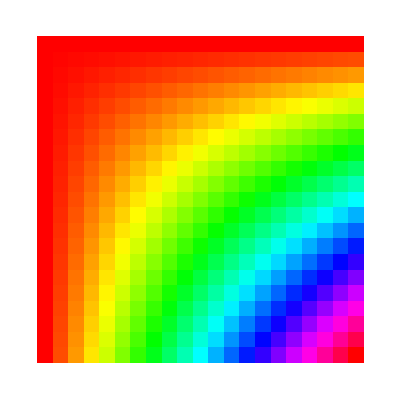

```mathematica
ArrayPlot[Table[x*y,{x,0,1,0.05},{y,0,1,0.05}],ColorFunction->(Hue[#]&) ]
```

13.8 Make an array plot of hue values x/y, where x and y each run from 1 to 50 in steps of 1.

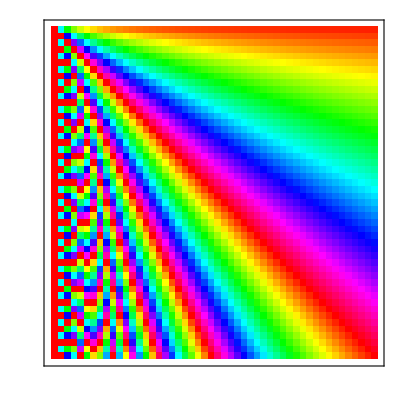

```mathematica
ArrayPlot[Table[Hue[x/y],{x,1,50},{y,1,50}],ColorFunction->Identity,Frame->True]
```

13.9 Make an array plot of the lengths of Roman numeral strings in a multiplication table up to 100×100.

```mathematica
ArrayPlot[Table[StringLength[RomanNumeral[x*y]],{x,100},{y,100}]]
```

-Graphics-

14.1 Make graphics of 5 concentric circles centered at {0, 0} with radii 1, 2, ... , 5.

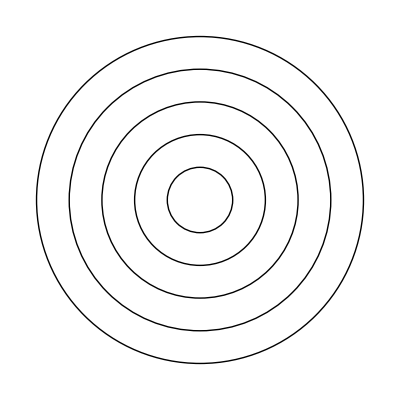

```mathematica
Graphics[Circle[{0,0},#]&/@Range[5]]
```

14.2 Make 10 concentric circles with random colors.

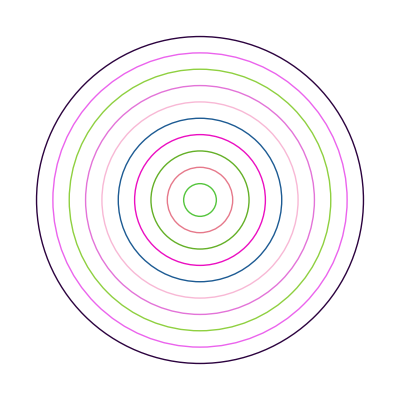

```mathematica
Graphics[Table[{RandomColor[],Circle[{0,0},n]},{n,10}]]
```

14.3 Make graphics of a 10×10 grid of circles with radius 1 centered at integer points {x, y}.

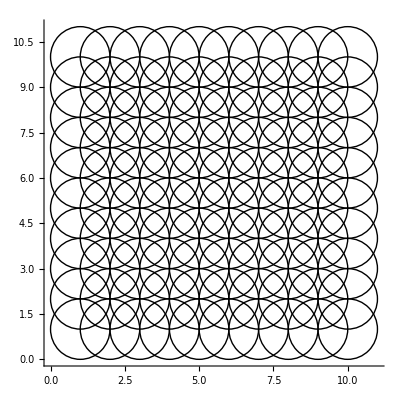

```mathematica
Graphics[Table[Circle[{x,y},1],{x,10},{y,10}],Axes->True]
```

14.4 Make a 10×10 grid of points with coordinates at integer positions up to 10.

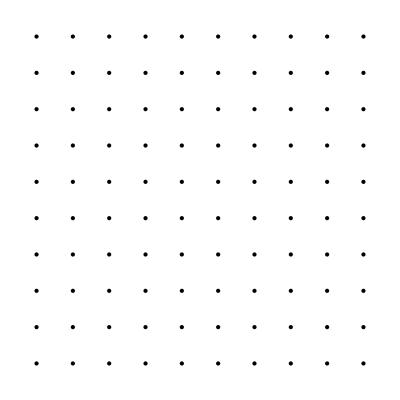

```mathematica
Graphics[Point[Flatten[Table[{x,y},{x,10},{y,10}],1]]]
```

14.5 Make a Manipulate with between 1 and 20 concentric circles.

```mathematica
Manipulate[Graphics[Table[Circle[{0,0},n],{n,num}],PlotRange->{{-20,20},{-20,20}}],{num,1,20,1}]
```

14.6 Place 50 spheres with random colors at random integer coordinates up to 10.

```mathematica
Graphics3D[Table[{RandomColor[],Sphere[RandomInteger[10,3]]},{50}]]
```

-Graphics3D-

14.7 Make an 11×11×11 array of spheres with RGB components ranging from 0 to 1. The spheres should be centered at integer coordinates, and should just touch each other.

```mathematica
Graphics3D[Table[{RGBColor[x/10,y/10,z/10],Sphere[{x,y,z},0.5]},{x,0,10},{y,0,10},{z,0,10}]]
```

-Graphics3D-

14.8 Make a Manipulate with t varying between −2 and +2 that contains circles of radius x centered at {t*x, 0} with x going from 1 to 10.

```mathematica
Manipulate[Graphics[Table[Circle[{t*x,0},x],{x,1,10}],PlotRange->{{-20,20},{-10,10}}],{t,-2,2}]
```

14.9 Make a 5×5 array of regular hexagons with size 1/2, centered at integer points.

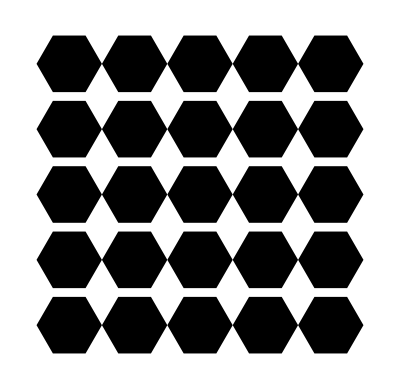

```mathematica
hexagon[{x_,y_},r_]:=Polygon[Table[{x+r Cos[2 Pi k/6],y+r Sin[2 Pi k/6]},{k,0,5}]];

Graphics[Table[hexagon[{x,y},1/2],{x,1,5},{y,1,5}]//Flatten]
```

14.10 Make a line in 3D that goes through 50 random points with integer coordinates randomly chosen up to 50.

```mathematica
Graphics3D[Line[Table[RandomInteger[50,3],{50}]]]
```

-Graphics3D-

14.11 Make a Manipulate of an icosahedron with side length varying from 1 to 2 and a dodecahedron with side length 1, both having opacity 0.5 and the same center.

```mathematica
Manipulate[Graphics3D[{{Opacity[0.5],Icosahedron[{0,0,0},s]},(*s sem chaves*){Opacity[0.5],Dodecahedron[{0,0,0},1]} (*1 sem chaves*)},PlotRange->All,Boxed->False],{s,1,2}]
```